```mathematica
Get["NeutronBeam/NeutronBeamDefinition.m"]
```

Check Trapezoid function

```mathematica
?TrapezNBeamNew
```

Global`TrapezNBeamNew

TrapezNBeamNew[xn_,{tw_,pl_,k1_,k2_,k3_}]:=Piecewise[{{0,xn<-tw/2},{k1 xn+(k1 tw)/2,-tw/2≤xn<-(2 k2 pl-2 k3 pl+(k1+k3) tw)/(2 (k1-k3))},{k2 xn+(-2 (k1-k2) (k2-k3) pl+(k1 (k2-2 k3)+k2 k3) tw)/(2 (k1-k3)),-(2 k2 pl-2 k3 pl+(k1+k3) tw)/(2 (k1-k3))≤xn<-(2 (-k1+k2) pl+(k1+k3) tw)/(2 (k1-k3))},{k3 xn-(k3 tw)/2,-(2 (-k1+k2) pl+(k1+k3) tw)/(2 (k1-k3))≤xn≤tw/2},{0,xn>tw/2}}]

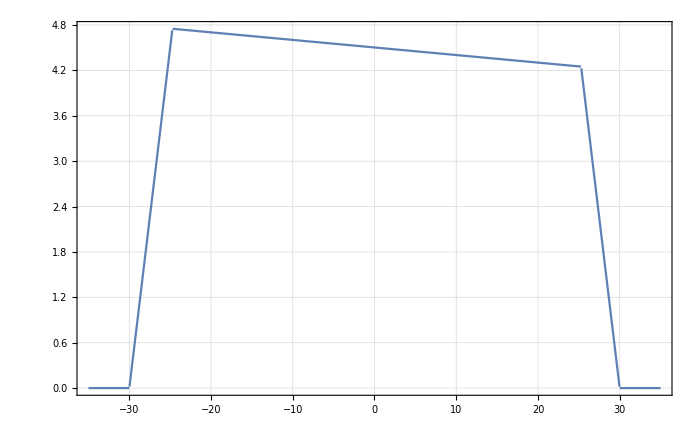

```mathematica
Plot[TrapezNBeamNew[xn,{60,50,0.9,-0.01,-0.9}],{xn,-35,35}]
```

### 2D

```mathematica
Plot3D[TrapezNBeamNew[xn,{60,50,0.9,-0.01,-0.9}]*TrapezNBeamNew[yn,{100,90,0.9,-0.01,-0.9}],{xn,-35,35},{yn,-55,55}]
```

-Graphics3D-

### is the norm of the 2D trapezoid the same as the 2 1D norms?

```mathematica
NIntegrate[TrapezNBeamNew[xn,{60,50,0.9,-0.01,-0.9}]*TrapezNBeamNew[yn,{100,90,0.9,-0.01,-0.9}],{xn,-35,35},{yn,-55,55}]
```

105892.

```mathematica
NIntegrate[TrapezNBeamNew[xn,{60,50,0.9,-0.01,-0.9}],{xn,-35,35}]
```

247.569

```mathematica
NIntegrate[TrapezNBeamNew[yn,{100,90,0.9,-0.01,-0.9}],{yn,-55,55}]
```

427.725

```mathematica
247.5694444444444*427.7250000000009
```

105892.

### yes

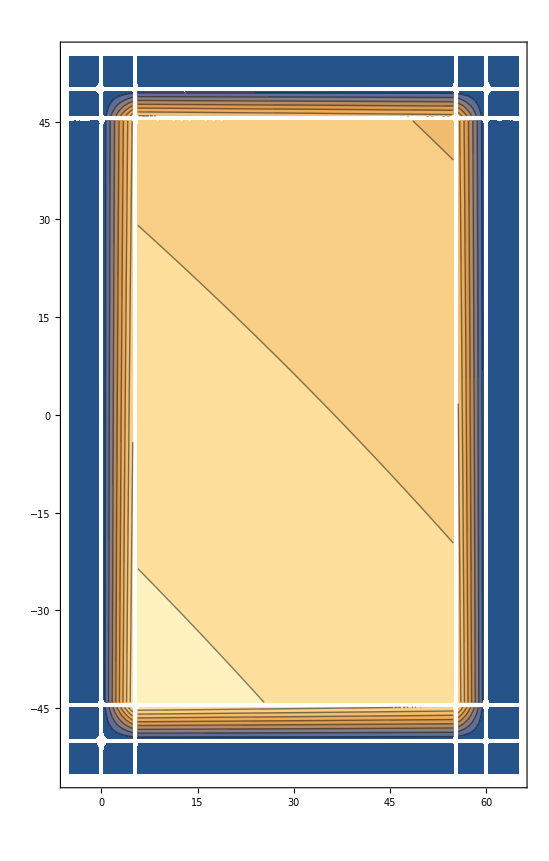

```mathematica
ContourPlot[TrapezNBeamNew[xn-30,{60,50,0.9,-0.01,-0.9}]*TrapezNBeamNew[yn,{100,90,0.9,-0.01,-0.9}],{xn,-5,65},{yn,-55,55},AspectRatio->Automatic]
```

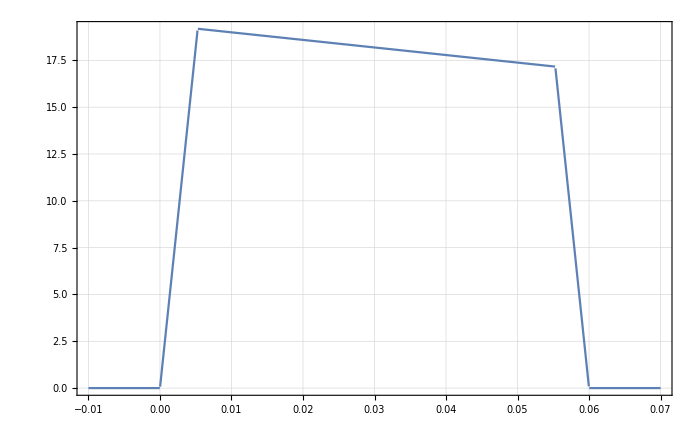

```mathematica
Plot[TrapezNBeamNewNormed[xn-0.030,{0.060,0.050,0.9,-0.01,-0.9}],{xn,-0.010,0.070}]
```

Integrand (has the x0 and y0 replacement rules in the 2D trapecoidal functions - as well as xOff/yOff)

```mathematica
Integrand2DArithBGradDetSpreadNBeam[b_?NumericQ,{xD_?NumericQ,yD_?NumericQ,phi_?NumericQ,p_?NumericQ,th0_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ},{xA_?NumericQ,yA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ,rA_?NumericQ},{R0_?NumericQ,G1_?NumericQ,G2_?NumericQ},{phiDV_,twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_}]:=

wmomNormedWb[λ0,κ0,b,p]*Sin[th0]*

TrapezNBeamNewNormed[(xD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Sin[phi])*Sqrt[rD/rRxB]+D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],R0,G1,G2]+rG[p,th0,rA*BRxB/rRxB]*Cos[phiDV]-xOff,{twx,plx,k1x,k2x,k3x}]*

TrapezNBeamNewNormed[(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB]+rG[p,th0,rA*BRxB/rRxB]*Sin[phiDV]-yOff,{twy,ply,k1y,k2y,k3y}]*

ArithApert[xA,yA,xOff,yOff,
(xD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Sin[phi])*Sqrt[rD/rRxB]+D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],R0,G1,G2],(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],
rG[p,theta2[th0,rA],rA*BRxB/rRxB]
]
```

```mathematica
Plot3D[Integrand2DArithBGradDetSpreadNBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}],{phiDV,0,2*Pi},{phi,0,2*Pi},AxesLabel->{"phiDV","phi","Integrand"}]
```

-Graphics3D-

### we first saw no phiDV dependence for varying xD. To investigate, we check, what parameter space xn goes into the nbeam function.

```mathematica
Plot3D[((xD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Sin[phi])*Sqrt[rD/rRxB]+D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],R,G1,G2]+rG[p,th0,rA*BRxB/rRxB]*Cos[phiDV]-xOff)/.
{xD->0.035,p->500000,th0->Pi/4,BRxB->0.2,rRxB->1,rD->1.,rA->1,alpha->Pi,yD->0.,R->1,G1->1,G2->1,xOff->0.04},{phiDV,0,2*Pi},{phi,0,2*Pi},PlotRange->{0,0.03}]
```

-Graphics3D-

### only for xD > 0.03, we hit the nbeam range limit of +0,03 m. Maybe, the integrand is there already completely zero for another reason (apert func?)

### above, we now did k2 unequal zero, then we should easier see an effect of nbeam through phiDV-> and we do for very strong k2’s

### now we just switch off neutron beam in integrand to directly compare

```mathematica
Integrand2DArithBGradDetSpreadNoBeam[b_?NumericQ,{xD_?NumericQ,yD_?NumericQ,phi_?NumericQ,p_?NumericQ,th0_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ},{xA_?NumericQ,yA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ,rA_?NumericQ},{R0_?NumericQ,G1_?NumericQ,G2_?NumericQ},{phiDV_,twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_}]:=

wmomNormedWb[λ0,κ0,b,p]*Sin[th0]*

ArithApert[xA,yA,xOff,yOff,
(xD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Sin[phi])*Sqrt[rD/rRxB]+D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],R0,G1,G2],(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],
rG[p,theta2[th0,rA],rA*BRxB/rRxB]
]
```

```mathematica
Plot3D[
{
Integrand2DArithBGradDetSpreadNoBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}],
Integrand2DArithBGradDetSpreadNBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}]
},{phiDV,0,2*Pi},{phi,0,2*Pi},AxesLabel->{"phiDV","phi","Integrand"},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[
{
100*Integrand2DArithBGradDetSpreadNoBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}],
Integrand2DArithBGradDetSpreadNBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}]
},{phiDV,0,2*Pi},{phi,0,2*Pi},AxesLabel->{"phiDV","phi","Integrand"}]
```

-Graphics3D-

### its just that the scale of the 2 integrands is completely different..

```mathematica
Integrand2DArithBGradDetSpreadNoBeam[0,{0.0,0,3.Pi/2,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{0,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}]
```

3.98526×10^-8

### one trapez function factors the integrand by a factor of 10, so a factor of at least 100 seems reasonable

# Option 3: Apert(x_traj_A,y_traj_A) with boole

## 3.1: With integration of xDV, yDV, ϕDV

```mathematica
ApertBoole[xtraj_,ytraj_,{xA_,yA_,xOff_,yOff_}]:=Boole[xtraj<xOff+xA/2&&xtraj>xOff-xA/2&&ytraj<yOff+yA/2&&ytraj>yOff-yA/2]
```

```mathematica
RepeatedTiming[ApertBoole[0.03,0.,{0.01,0.035,0.03,0.}]]
```

{5.84×10^-6,1}

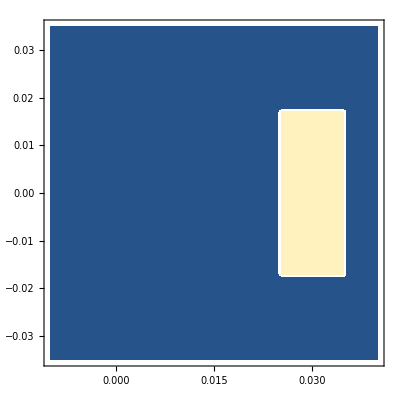

```mathematica
ContourPlot[ApertBoole[xtraj,ytraj,{0.01,0.035,0.03,0.}],{xtraj,-0.01,0.04},{ytraj,-0.035,0.035}]
```

```mathematica
ClearAll[xGCA,yGCA]
```

```mathematica
xGCA[xDV_,phiDV_,p_,th0_,BRxB_,rRxB_,rA_]:=(xDV-rG[p,th0,BRxB/rRxB]*Cos[phiDV])*Sqrt[1/rA]
yGCA[yDV_,phiDV_,p_,th0_,BRxB_,rRxB_,rA_]:=(yDV-rG[p,th0,BRxB/rRxB]*Sin[phiDV])*Sqrt[1/rA]
```

```mathematica
?D1stBPolyGrad
```

Global`D1stBPolyGrad

D1stBPolyGrad[p_,alpha_,th0_,BRxB_,rRxB_,y0_,R_,G1_,G2_]:=(p alpha fReduced[th0,rRxB])/(c BpolynomGrad[y0,BRxB,R,G1,G2])

```mathematica
ClearAll[DeltaxDV,DeltayDV]
```

```mathematica
DeltayDV[phiDV_,yD_,p_,th0_,BRxB_,rRxB_,rA_,rD_,phiDet_]:=(yD-rG[p,th0,rD*BRxB/rRxB]*Sin[phiDet])*Sqrt[rD/rRxB]*Sqrt[rA]+rG[p,th0,BRxB/rRxB]*Sin[phiDV]
DeltaxDV[phiDV_,yDV_,xD_,p_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_,R_,G1_,G2_]:=((xD-rG[p,th0,rD*BRxB/rRxB]*Cos[phiDet])*Sqrt[rD/rRxB]-D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,yGCA[yDV,phiDV,p,th0,BRxB,rRxB,rA],R,G1,G2])*Sqrt[rA]+rG[p,th0,BRxB/rRxB]*Cos[phiDV]
```

```mathematica
ClearAll[DeltaxDV2]
```

```mathematica
DeltaxDV2[phiDV_,yD_,xD_,p_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_,R_,G1_,G2_]:=DeltaxDV[phiDV,DeltayDV[phiDV,yD,p,th0,BRxB,rRxB,rA,rD,phiDet],xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]
```

```mathematica
DeltaxDV2[phiDV,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]
```

(3.34448×10^-9 p rRxB Cos[phiDV] Sin[th0])/BRxB+√rA (√(rD/rRxB) (xD-(3.34448×10^-9 p rRxB Cos[phiDet] Sin[th0])/(BRxB rD))-(alpha p (2-rRxB Sin[th0]^2))/(599584916 √(1-rRxB Sin[th0]^2) (BRxB-(BRxB G1 √(1/rA) (0.+√rA √(rD/rRxB) (yD-(3.34448×10^-9 p rRxB Sin[phiDet] Sin[th0])/(BRxB rD))))/R+(BRxB G2 (0.+√rA √(rD/rRxB) (yD-(3.34448×10^-9 p rRxB Sin[phiDet] Sin[th0])/(BRxB rD)))^2)/(R^2 rA))))

```mathematica
DeltaxDV2[0,0,0.,700000,Pi/4,Pi,0.2,1,1,1,0,1,1,1]
```

-0.0389021

```mathematica
xA[phiDV_,phiA_,yD_,xD_,p_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_,R_,G1_,G2_]:=xGCA[DeltaxDV2[phiDV,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],phiDV,p,th0,BRxB,rRxB,rA]+rG[p,th0,rA*BRxB/rRxB]*Cos[phiA]
```

```mathematica
yA[phiDV_,phiA_,yD_,p_,th0_,BRxB_,rRxB_,rA_,rD_,phiDet_]:=yGCA[DeltayDV[phiDV,yD,p,th0,BRxB,rRxB,rA,rD,phiDet],phiDV,p,th0,BRxB,rRxB,rA]+rG[p,th0,rA*BRxB/rRxB]*Sin[phiA]
```

```mathematica
Integrand2DwNBeamv31[b_,phiDV_,phiA_,yD_,xD_,p_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_,R_,G1_,G2_,{twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_},{xAA_,yAA_,xOff_,yOff_}]:=
wmomNormedWb[λ0,κ0,b,p]*Sin[th0]*

TrapezNBeamNewNormed[DeltaxDV2[phiDV,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],{twx,plx,k1x,k2x,k3x}]*
TrapezNBeamNewNormed[DeltayDV[phiDV,yD,p,th0,BRxB,rRxB,rA,rD,phiDet],{twy,ply,k1y,k2y,k3y}]*

ApertBoole[xA[phiDV,phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],yA[phiDV,phiA,yD,p,th0,BRxB,rRxB,rA,rD,phiDet],{xAA,yAA,xOff,yOff}]
```

### oh, drift was defined in positive direction, thats why we have to choose positive xD currently

```mathematica
Plot3D[
Integrand2DwNBeamv31[0.,phiDV,phiDV,0.,0.03,p,Pi/8,Pi,0.2,1,1,1,phiDV,1,1,1,{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],{phiDV,0,2*Pi},{p,0,pmax},PlotPoints->50]
```

-Graphics3D-

```mathematica
RepeatedTiming[Integrand2DwNBeamv31[0.,0,0,0.,0.03,600000,Pi/8,Pi,0.2,1,1,1,0,1,1,1,{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}]]
```

{0.00043,0.000124314}

```mathematica
150000*0.00043
```

64.5

```mathematica
NIntegrate[
Integrand2DwNBeamv31[0.,phiDV,phiDV,0.,0.03,p,th0,Pi,0.2,1.,1.,1.,phiDV,1.,1.,1.,{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],{th0,0,Pi/4},{phiDV,0,2*Pi},{p,0,pmax},PrecisionGoal->3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 111.254 and 0.120373 for the integral and error estimates.

111.254

## now you can again get limits for p by investigating aperture limits as well as neutron beam limits

```mathematica
xA[phiDV,phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]
```

(3.34448×10^-9 p rRxB Cos[phiA] Sin[th0])/(BRxB rA)+√(1/rA) (0.+√rA (√(rD/rRxB) (xD-(3.34448×10^-9 p rRxB Cos[phiDet] Sin[th0])/(BRxB rD))-(alpha p (2-rRxB Sin[th0]^2))/(599584916 √(1-rRxB Sin[th0]^2) (BRxB-(BRxB G1 √(1/rA) (0.+√rA √(rD/rRxB) (yD-(3.34448×10^-9 p rRxB Sin[phiDet] Sin[th0])/(BRxB rD))))/R+(BRxB G2 (0.+√rA √(rD/rRxB) (yD-(3.34448×10^-9 p rRxB Sin[phiDet] Sin[th0])/(BRxB rD)))^2)/(R^2 rA)))))

```mathematica
testsolve=Solve[0.005==xA[phiDV,phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],p]
```

{{p→-((0.333333 BRxB rD 1 Csc[th0] (-4.4819×10^16 G1 R √(1/rA) √rA √(rD/rRxB) rRxB Cos[phiA]+8.96379×10^16 G2 rD yD Cos[phiA]+4.4819×10^16 G1 R rA Cos[phiDet]-8.96379×10^16 G2 √(1/rA) rA^1 √(rD/rRxB) yD Cos[phiDet]+2.24095×10^14 G2 rA Sin[phiDet]-4.4819×10^16 G2 √(1/rA) rA^(3/2) √(rD/rRxB) xD Sin[phiDet]))/(G2 rRxB (-1.49896×10^8 rD Cos[phiA]+1.49896×10^8 √(1/rA) rA^(3/2) √(rD/rRxB) Cos[phiDet])))+1/(G2 3 1^1)-((0.132283+0.229122 ⅈ) Csc[phiDet]^2 Csc[th0]^3 (1)^(1/3))/(G2 rRxB^3 (-1.49896×10^8 rD Cos[phiA]+1.49896×10^8 3 Cos[phiDet]) √(1.-1. rRxB Sin[th0]^2))},{p→1},{p→1}}
 |  |  |  |

```mathematica
testsolve/.{phiDV->0,phiA->0,yD->0,xD->0.03,th0->Pi/4,alpha->Pi,BRxB->0.2,rRxB->1,rA->1,rD->1,phiDet->0,R->1,G1->1,G2->1}
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √2 ComplexInfinity ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) 2 √2 ComplexInfinity ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) 2 √2 ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{p→Indeterminate},{p→Indeterminate},{p→Indeterminate}}

```mathematica
Solve[0.005==xA[phiDV,phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]/.{phiDV->0,phiA->0,yD->0,xD->0.03,th0->Pi/4,alpha->Pi,BRxB->0.2,rRxB->1,rA->1,rD->1,phiDet->0,R->1,G1->1,G2->1},p]
```

{{p→449847.}}

```mathematica
Solve[-0.005==xA[phiDV,phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]/.{phiDV->0,phiA->0,yD->0,xD->0.03,th0->Pi/4,alpha->Pi,BRxB->0.2,rRxB->1,rA->1,rD->1,phiDet->0,R->1,G1->1,G2->1},p]
```

{{p→629785.}}

### so we have to put in numeric values to solve. it depends on phi, so we might have to change integration order, phi after p

```mathematica
ClearAll[pminNBeam]
```

```mathematica
pminNBeam[phiDV_,phiA_,yD_,xD_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_,R_,G1_,G2_,xOff_,xAA_]:=Solve[xOff+xAA/2==xA[phiDV,phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],p][[1,1,2]]
```

```mathematica
pminNBeam[0.,0.,0.,0.03,Pi/8,Pi,0.2,1,1,1,0.,1,1,1,0.,0.01]
```

475643.

```mathematica
Plot3D[pminNBeam[phiDV,phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],{th0,0,Pi/4},{phiDV,0,2Pi}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

```mathematica
pmaxNBeam[phiDV_,phiA_,yD_,xD_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_,R_,G1_,G2_,xOff_,xAA_]:=Solve[xOff-xAA/2==xA[phiDV,phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],p][[1,1,2]]
```

```mathematica
pmaxNBeam[0.,0.,0.,0.03,Pi/8,Pi,0.2,1,1,1,0.,1,1,1,0.,0.01]
```

665900.

```mathematica
Plot3D[pmaxNBeamCases[phiDV,phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],{th0,0,Pi/4},{phiDV,0,2Pi},PlotRange->All]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

```mathematica
ClearAll[pminNBeamCases,pmaxNBeamCases]
```

```mathematica
pminNBeamCases[phiDV_?NumericQ,phiA_?NumericQ,yD_,xD_,th0_?NumericQ,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_?NumericQ,R_,G1_,G2_,xOff_,xAA_]:=Module[
{pminlocal=pminNBeam[phiDV,phiA,yD,xD,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,xOff,xAA]},
Piecewise[
{
{0,pminlocal<0},
{pmax,pminlocal>pmax}
},
pminlocal
]
]
```

```mathematica
pmaxNBeamCases[phiDV_?NumericQ,phiA_?NumericQ,yD_,xD_,th0_?NumericQ,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_?NumericQ,R_,G1_,G2_,xOff_,xAA_]:=Module[
{pmaxlocal=pmaxNBeam[phiDV,phiA,yD,xD,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,xOff,xAA]},
Piecewise[
{
{0,pmaxlocal<0},
{pmax,pmaxlocal>pmax}
},
pmaxlocal
]
]
```

```mathematica
NIntegrate[
Integrand2DwNBeamv31[0.,phiDV,phiDV,0.,0.03,p,th0,Pi,0.2,1.,1.,1.,phiDV,1.,1.,1.,{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],{th0,0,Pi/4},{phiDV,0,2*Pi},
{p,pminNBeamCases[phiDV,phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->False}]
```

111.298

```mathematica
testTable=ParallelTable[{
xD,
yD,
NIntegrate[
Integrand2DwNBeamv31[0.,phiDV,phiDV,yD,xD,p,th0,Pi,0.2,1.,1.,1.,phiDV,1.,1.,1.,{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],{th0,0,Pi/4},{phiDV,0,2*Pi},
{p,pminNBeamCases[phiDV,phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->False}]},{xD,-0.005,0.07,0.005},{yD,-0.045,0.045,0.01}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{{-0.005,-0.045,0.},{-0.005,-0.035,0.},{-0.005,-0.025,0.},{-0.005,-0.015,0.},{-0.005,-0.005,0.},{-0.005,0.005,0.},{-0.005,0.015,0.},{-0.005,0.025,0.},{-0.005,0.035,0.},{-0.005,0.045,0.}},{{0.,-0.045,0.},{0.,-0.035,0.},{0.,-0.025,0.},{0.,-0.015,0.880255},{0.,-0.005,1.10026},{0.,0.005,1.3077},{0.,0.015,1.50333},{0.,0.025,0.},{0.,0.035,0.},{0.,0.045,0.}},{{0.005,-0.045,0.},{0.005,-0.035,0.},{0.005,-0.025,0.},{0.005,-0.015,6.37679},{0.005,-0.005,7.96956},{0.005,0.005,9.47081},{0.005,0.015,10.8858},{0.005,0.025,0.},{0.005,0.035,0.},{0.005,0.045,0.}},{{0.01,-0.045,0.},{0.01,-0.035,0.},{0.01,-0.025,0.},{0.01,-0.015,19.0956},{0.01,-0.005,23.8879},{0.01,0.005,28.4135},{0.01,0.015,32.6872},{0.01,0.025,0.},{0.01,0.035,0.},{0.01,0.045,0.}},{{0.015,-0.045,0.},{0.015,-0.035,0.},{0.015,-0.025,0.},{0.015,-0.015,36.7162},{0.015,-0.005,46.0178},{0.015,0.005,54.8368},{0.015,0.015,63.1972},{0.015,0.025,0.},{0.015,0.035,0.},{0.015,0.045,0.}},{{0.02,-0.045,0.},{0.02,-0.035,0.},{0.02,-0.025,0.},{0.02,-0.015,55.2055},{0.02,-0.005,69.3863},{0.02,0.005,82.9099},{0.02,0.015,95.8036},{0.02,0.025,0.},{0.02,0.035,0.},{0.02,0.045,0.}},{{0.025,-0.045,0.},{0.025,-0.035,0.},{0.025,-0.025,0.},{0.025,-0.015,70.5498},{0.025,-0.005,89.0123},{0.025,0.005,106.756},{0.025,0.015,123.801},{0.025,0.025,0.},{0.025,0.035,0.},{0.025,0.045,0.}},{{0.03,-0.045,0.},{0.03,-0.035,0.},{0.03,-0.025,0.},{0.03,-0.015,79.5382},{0.03,-0.005,100.868},{0.03,0.005,121.573},{0.03,0.015,141.657},{0.03,0.025,0.},{0.03,0.035,0.},{0.03,0.045,0.}},{{0.035,-0.045,0.},{0.035,-0.035,0.},{0.035,-0.025,0.},{0.035,-0.015,80.2426},{0.035,-0.005,102.473},{0.035,0.005,124.337},{0.035,0.015,145.812},{0.035,0.025,0.},{0.035,0.035,0.},{0.035,0.045,0.}},{{0.04,-0.045,0.},{0.04,-0.035,0.},{0.04,-0.025,0.},{0.04,-0.015,72.2735},{0.04,-0.005,93.2162},{0.04,0.005,114.18},{0.04,0.015,135.113},{0.04,0.025,0.},{0.04,0.035,0.},{0.04,0.045,0.}},{{0.045,-0.045,0.},{0.045,-0.035,0.},{0.045,-0.025,0.},{0.045,-0.015,56.9045},{0.045,-0.005,74.5133},{0.045,0.005,92.5833},{0.045,0.015,111.044},{0.045,0.025,0.},{0.045,0.035,0.},{0.045,0.045,0.}},{{0.05,-0.045,0.},{0.05,-0.035,0.},{0.05,-0.025,0.},{0.05,-0.015,37.1288},{0.05,-0.005,49.8776},{0.05,0.005,63.4633},{0.05,0.015,77.8185},{0.05,0.025,0.},{0.05,0.035,0.},{0.05,0.045,0.}},{{0.055,-0.045,0.},{0.055,-0.035,0.},{0.055,-0.025,0.},{0.055,-0.015,17.6777},{0.055,-0.005,24.9472},{0.055,0.005,33.2052},{0.055,0.015,42.4291},{0.055,0.025,0.},{0.055,0.035,0.},{0.055,0.045,0.}},{{0.06,-0.045,0.},{0.06,-0.035,0.},{0.06,-0.025,0.},{0.06,-0.015,4.65771},{0.06,-0.005,7.23353},{0.06,0.005,10.5271},{0.06,0.015,14.5869},{0.06,0.025,0.},{0.06,0.035,0.},{0.06,0.045,0.}},{{0.065,-0.045,0.},{0.065,-0.035,0.},{0.065,-0.025,0.},{0.065,-0.015,0.289638},{0.065,-0.005,0.604699},{0.065,0.005,1.12825},{0.065,0.015,1.92978},{0.065,0.025,0.},{0.065,0.035,0.},{0.065,0.045,0.}},{{0.07,-0.045,0.},{0.07,-0.035,0.},{0.07,-0.025,0.},{0.07,-0.015,0.},{0.07,-0.005,0.000608414},{0.07,0.005,0.00363481},{0.07,0.015,0.0141364},{0.07,0.025,0.},{0.07,0.035,0.},{0.07,0.045,0.}}}

```mathematica
ListPlot3D[Flatten[%,1]]
```

-Graphics3D-